```mathematica
Integrate[f[x,a],{x,0,1},{a,0,1}]
```

∫_0^1 ∫_0^1 f[x,a]ⅆaⅆx

```mathematica
Integrate[f[x,a],x,a]
```

∫∫f[x,a]ⅆaⅆx

```mathematica
∫∫_A f[x,a]ⅆaⅆx
```

Integrate::intnest: The integral ∫∫_A f[x,a]ⅆaⅆx cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
Cross[{x,f[x],0},{x,g[x],0}]
```

{0,0,-x f[x]+x g[x]}

```mathematica
Cross[{x,x,0},{x,x x,0}]
```

{0,0,-x^2+x^3}

```mathematica
-x^2+x^3
```

-x^2+x^3

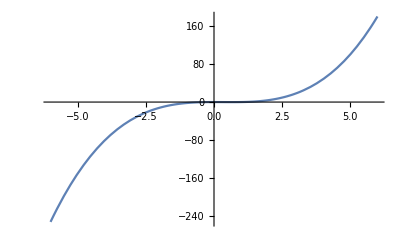

```mathematica
Plot[-x^2+x^3,{x,-6.,6.}]
```

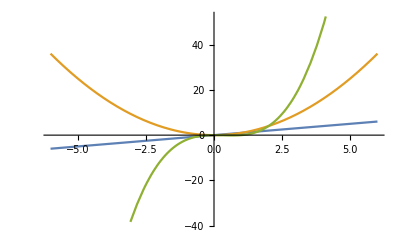

```mathematica
Plot[{x,x x,-x^2+x^3},{x,-6.,6.}]
```

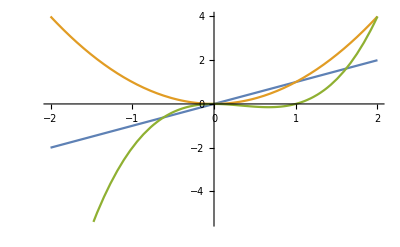

```mathematica
Plot[{x,x x,-x^2+x^3},{x,-2,2}]
```

```mathematica
Cross[A,B]
```

A×B

```mathematica
Cross[(∂x)/(∂s),(∂x)/(∂t)]
```

Derivative::novar: ∂x cannot be interpreted. A partial derivative requires a subscript differentiation variable.

```mathematica
Cross[(∂{Subscript[x, 1][t],Subscript[y, 1][t],Subscript[z, 1][t]})/(∂s),(∂{Subscript[x, 2][t],Subscript[y, 2][t],Subscript[z, 2][t]})/(∂t)]
```

Derivative::novar: ∂{x_1[t],y_1[t],z_1[t]} cannot be interpreted. A partial derivative requires a subscript differentiation variable.

```mathematica
Dt[A==x y]
```

Dt[A]==y Dt[x]+x Dt[y]

```mathematica
Dt[A[t]==x [t]y[t]]
```

Dt[t] A'[t]==Dt[t] y[t] x'[t]+Dt[t] x[t] y'[t]

```mathematica
TraditionalForm[Dt[t] A'[t]==Dt[t] y[t] x'[t]+Dt[t] x[t] y'[t]]
```

ⅆt A'(t)==y(t) ⅆt x'(t)+x(t) ⅆt y'(t)

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
Integrate[f'[g[x]] g'[x],x]
```

f[g[x]]

```mathematica
f'[g[x]]==a'[x]
```

f'[g[x]]==a'[x]

```mathematica
Integrate[f'[g[x]],x]==Integrate[a'[x],x]
```

∫f'[g[x]]ⅆx==a[x]

```mathematica
Integrate[f'[g[x]]g'[x],x]==Integrate[a'[x]g'[x],x]
```

f[g[x]]==∫a'[x] g'[x]ⅆx